## ^183Au - Wobbling Motion

### Theoretical results → Numerical Implementation

```mathematica
ClearAll["Global*`"]
```

### Odd-particles & other functions

```mathematica
j1=N[13/2];
I01=N[13/2];
j2=N[9/2];
I02=N[9/2];
IF[MOI_]:=1/(2*MOI);
RAD[angle_]:=angle*π/180;
```

```mathematica
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)(I+j)/2+A1*(I-j)^2-V*(2j-1)/(j+1)*Sin[γ+π/6];
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-1*(((2I-1)*(A3-A1)+2j*A1)*((2I-1)*(A2-A1)+2j*A1)+8*A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=((((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))-4I*j*A3^2)*(((2I-1)*(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ])-4I*j*A2^2));
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]-Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]+Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Energy[nw1_,nw2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](nw1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](nw2+1/2);
ExcEn[nw1_,nw2_,I0_,I_,j_,A1_,A2_,A3_,V_,γ_]:=Energy[nw1,nw2,I,j,A1,A2,A3,V,γ]-Energy[0,0,I0,j,A1,A2,A3,V,γ];
band1Plus[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[0,0,I01,I,j1,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
band2Plus[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[1,0,I01,I,j1,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
(*TO DO -> ADD ENERGY EXPRESSIONS FOR THE NEGATIVE PARITY BANDS*)
band1Negative[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[0,0,I02,I,j2,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
band2Negative[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[1,0,I02,I,j2,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
```

#### Positive Parity Bands - Experimental data

```mathematica
s1Plus=Table[N[i],{i,6.5,32.5,2}];
s2Plus=Table[N[i],{i,11.5,21.5,2}];
yrastPlus=N[{702,867,1151,1530,1983,2492,3049,3655,4308,4986,5677,6375,7103,7848}/1000];
tw1Plus=N[{1739,2178,2684,3243,3840,4464}/1000];
e0Plus=yrastPlus[[1]];
yrastPlus=Table[yrastPlus[[i]]-e0Plus,{i,1,Length[yrastPlus]}];
tw1Plus=Table[tw1Plus[[i]]-e0Plus,{i,1,Length[tw1Plus]}];
```

#### Positive Parity Bands - χ^2 function "RMS-> "0.0735616" P -> "{83.4294,3.64419,25.7625,1.99236,19.}

```mathematica
(*chi2FuncPlus[I1_,I2_,I3_,V_,γ_]:=If[Im[Sqrt[1/(Length[s1Plus]+Length[s2Plus]+1)(Sum[(yrastPlus[[i]]-band1Plus[s1Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Plus]}]+Sum[(tw1Plus[[i]]-band2Plus[s2Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Plus]}])]]==0,Sqrt[1/(Length[s1Plus]+Length[s2Plus]+1)(Sum[(yrastPlus[[i]]-band1Plus[s1Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Plus]}]+Sum[(tw1Plus[[i]]-band2Plus[s2Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Plus]}])],10^7];
minChi2Plus=NMinimize[{chi2FuncPlus[I1,I2,I3,V,γ],1≤I1≤90&&1≤I2≤90&&1≤I3≤90&&0.01≤V≤10.0&&19≤γ≤25},{I1,I2,I3,V,γ}];
paramSetPlus=Values@minChi2Plus[[2]];
rmsValuePLus=minChi2Plus[[1]];*)
paramSetPlus={83.42941524535888,3.644193995633027,25.76246065133313,1.9923557518833606,19.};
rmsValuePLus=0.07356158733901914;
Print["RMS-> ",rmsValuePLus,"\nP -> ",paramSetPlus]
```

RMS-> 0.0735616
P -> {83.4294,3.64419,25.7625,1.99236,19.}

#### Negative parity bands - Experimental data

```mathematica
s1Negative=Table[N[i],{i,9/2,53/2,2}];
s2Negative=Table[N[i],{i,19/2,51/2,2}];
yrastNegative=N[{12.78,232,566,990,1492,2063,2690,3358,4050,4760,5497,6242}/1000];
tw1Negative=N[{1056,1488,1987,2540,3148,3796,4457,5133,5912}/1000];
e0Negative=yrastNegative[[1]];
yrastNegative=Table[yrastNegative[[i]]-e0Negative,{i,1,Length[yrastNegative]}];
tw1Negative=Table[tw1Negative[[i]]-e0Negative,{i,1,Length[tw1Negative]}];
```

#### Negative Parity Bands - χ^2 function

```mathematica
(*chi2FuncNegative[I1_,I2_,I3_,V_,γ_]:=If[Im[Sqrt[1/(Length[s1Negative]+Length[s2Negative]+1)(Sum[(yrastNegative[[i]]-band1Negative[s1Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Negative]}]+Sum[(tw1Negative[[i]]-band2Negative[s2Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Negative]}])]]==0,Sqrt[1/(Length[s1Negative]+Length[s2Negative]+1)(Sum[(yrastNegative[[i]]-band1Negative[s1Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Negative]}]+Sum[(tw1Negative[[i]]-band2Negative[s2Negative[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Negative]}])],10^9];
minChi2Negative=NMinimize[{chi2FuncNegative[I1,I2,I3,V,γ],1≤I1≤90&&1≤I2≤90&&1≤I3≤90&&0.01≤V≤10.0&&15≤γ≤30},{I1,I2,I3,V,γ}];
paramSetNegative=Values@minChi2Negative[[2]];
rmsValueNegative=minChi2Negative[[1]];
Print["RMS-> ",rmsValueNegative,"\nP -> ",paramSetNegative]*)
```

```mathematica
(*Print["********** BAND 1 - POSITIVE PARITY **********"]
Do[Print[s1Plus[[i]]," ",yrastPlus[[i]]," ",band1Plus[s1Plus[[i]],paramSetPlus[[1]],paramSetPlus[[2]],paramSetPlus[[3]],paramSetPlus[[4]],paramSetPlus[[5]]]],{i,1,Length[s1Plus]}]
Print["********** BAND 2 - POSITIVE PARITY **********"]
Do[Print[s2Plus[[i]]," ",tw1Plus[[i]]," ",band2Plus[s2Plus[[i]],paramSetPlus[[1]],paramSetPlus[[2]],paramSetPlus[[3]],paramSetPlus[[4]],paramSetPlus[[5]]]],{i,1,Length[s2Plus]}]*)
```

## Plot data

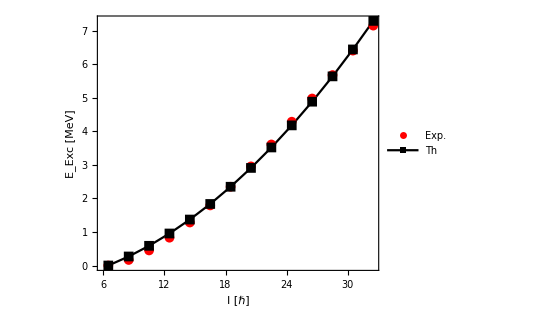

```mathematica
plotFunction[band_,params_,spins_,expData_]:=ListPlot[{Table[{spins[[i]],expData[[i]]},{i,1,Length[spins]}],Table[{spins[[i]],band[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}]},Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"I [ℏ]","E_Exc [MeV]"},PlotLegends->Placed[{"Exp.","Th"},{0.25,0.75}],FrameStyle->Directive[Thick,Black],LabelStyle->{19,Black,Bold,FontFamily->"Times"},Joined->{False, True},PlotStyle->{Red,Black},PlotMarkers->{Automatic, Medium}];
pPlus=plotFunction[band1Plus,paramSetPlus,s1Plus,yrastPlus];
Show[pPlus]
(*plotFunction[band2Plus,paramSetPlus,s2Plus,tw1Plus]*)
```

## Test environment for the energy sub-terms

```mathematica
(*Table[Omega1[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]
Table[Omega2[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]
Table[B1[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]
Table[C1[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]*)
```